```mathematica
localdir = "C:\\Users\\tramiada\\OneDrive\\Projects\\et3\\IBM\\";
asz = 12;th = 1.5;
```

## plotting landscape without aggregation

```mathematica
(* Plotting pre and post destruction *)
size= 4; lambda= 0.2;Fig= {};

dap=Import[localdir<>"patch_data_1.csv"];
das=Import[localdir<>"resource_unit_data_1.csv"];

Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda,
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{(*Thickness[0.01],*)Hue[dap[[i,3]]],Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
f2=Show[Graphics[Table[{Hue[das[[i,3]]],Disk[das[[i,{1,2}]],0.01]},{i,Length[das]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
figpre =Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"],PlotRange->{{0,3},{0,3}}];

dap=Import[localdir<>"patch_data_2.csv"];
das=Import[localdir<>"resource_unit_data_2.csv"];

lambda= 0.2 Sqrt[1];
Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda,
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{(*Thickness[0.01],*)Hue[dap[[i,3]]],Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
f2=Show[Graphics[Table[{Hue[das[[i,3]]],Disk[das[[i,{1,2}]],0.01]},{i,Length[das]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
figpost =Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"],PlotRange->{{0,3},{0,3}}];
```

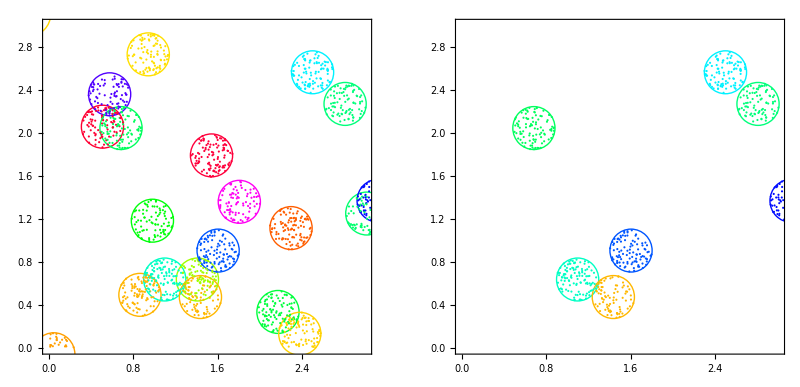

```mathematica
GraphicsGrid[{{figpre,figpost}},ImageSize->800]
```

```mathematica
(* Plotting pre and post destruction *)
size= 4; lambda= 0.2;Fig= {};

dap=Import[localdir<>"patch_data_1.csv"];
das=Import[localdir<>"resource_unit_data_1.csv"];

Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda,
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{(*Thickness[0.01],*)Hue[dap[[i,3]]],Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
f2=Show[Graphics[Table[{Hue[das[[i,3]]],Disk[das[[i,{1,2}]],0.01]},{i,Length[das]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
figpre =Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"],PlotRange->{{0,3},{0,3}}];

dap=Import[localdir<>"patch_data_1.csv"];
das=Import[localdir<>"resource_unit_data_2.csv"];

lambda= 0.1;
Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda,
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{(*Thickness[0.01],*)Hue[dap[[i,3]]],Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
f2=Show[Graphics[Table[{Hue[das[[i,3]]],Disk[das[[i,{1,2}]],0.01]},{i,Length[das]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
figpost =Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"],PlotRange->{{0,3},{0,3}}];
```

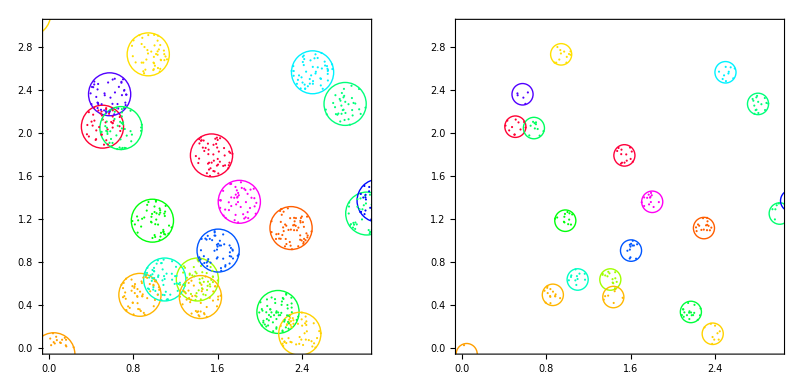

```mathematica
GraphicsGrid[{{figpre,figpost}},ImageSize->800]
```

## plotting landscape with aggregation

```mathematica
(* Plotting pre and post destruction *)
size= 6; lambda= 0.1;Fig= {};

dap=Import[localdir<>"patch_data_1.csv"];
das=Import[localdir<>"resource_unit_data_1.csv"];

Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda,
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{(*Thickness[0.01],*)Hue[dap[[i,3]]],Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
f2=Show[Graphics[Table[{Hue[das[[i,3]]],Disk[das[[i,{1,2}]],0.03]},{i,Length[das]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
figpre =Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"]];

dap=Import[localdir<>"patch_data_1.csv"];
das=Import[localdir<>"resource_unit_data_2.csv"];

Do[
xx=dap[[i,1]];
yy=dap[[i,2]];
zz=dap[[i,3]];
If[xx<lambda,
AppendTo[dap,{xx+size,yy,zz}]];
If[size-xx<lambda,
AppendTo[dap,{xx-size,yy,zz}]];
If[yy<lambda,
AppendTo[dap,{xx,yy+size,zz}]];
If[size-yy<lambda,
AppendTo[dap,{xx,yy-size,zz}]];
If[xx<lambda && yy<lambda,
AppendTo[dap,{xx+lambda,yy+lambda,zz}]];
If[xx-size<lambda &&yy-size<lambda,
AppendTo[dap,{xx-size,yy-size,zz}]
];
,{i,Length[dap]}];

f1=Show[Graphics[Table[{(*Thickness[0.01],*)Hue[dap[[i,3]]],Circle[dap[[i,{1,2}]],lambda]},{i,Length[dap]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
f2=Show[Graphics[Table[{Hue[das[[i,3]]],Disk[das[[i,{1,2}]],0.03]},{i,Length[das]}],PlotRange->{{0,size},{0,size}},PlotRangeClipping->True]];
figure1=Show[f1,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];

figure2=Show[f2,Frame->True,FrameStyle->Directive[asz,Black,"Arial"]];
figpost =Show[figure1,figure2,FrameStyle->Directive[asz,Black,AbsoluteThickness[th ],"Arial"]];
```